# 2D Nonlinear Systems - Local Analysis & Phase Plane

## Example #1

Consider the system given by 
ẋ = f(x,y)        where   f(x,y) = 2x + 4x y
ẏ = g(x,y)      where   g(x,y)= 6xy - 8y
We would like to (1) conduct local analysis, and (2) graph the phase plane to validate our local analysis conclusions.

### Local Analysis

```mathematica
f[x_,y_] = 2x + 4 x y;
g[x_,y_] = 6x y - 8 y;
```

```mathematica
eqPts = Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

{{x→4/3,y→-1/2},{x→0,y→0}}

```mathematica
DF[xs_,ys_] = {{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}/.{x->xs,y->ys};
```

```mathematica
For[j = 1,j≤Length[eqPts],j++,
Print[];
Print["==============================================================================================="];
Print["At the equilibrium point ",eqPts[[j]]," the eigensystem is given by ",MatrixForm[Eigensystem[DF[x,y]/.eqPts[[j]]]]];
Print["==============================================================================================="];
Print[];
]
```

===============================================================================================

At the equilibrium point {x→4/3,y→-1/2} the eigensystem is given by (4 ⅈ | -4 ⅈ
{-(4 ⅈ)/3,1} | {(4 ⅈ)/3,1})

===============================================================================================

===============================================================================================

At the equilibrium point {x→0,y→0} the eigensystem is given by (-8 | 2
{0,1} | {1,0})

===============================================================================================

### Comparing the Local Analysis with the Phase Plane

First, let’s create a loop that iterates over each of the equilibrium points.  We will plot the eigenvectors

```mathematica
For[j=1,j≤Length[eqPts],j++,
esys = Eigensystem[DF[x,y]/.eqPts[[j]]];
Subscript[evPlots, j]=ParametricPlot[esys[[2]]*s + Table[{x,y}/.eqPts[[j]] ,{k,1,2}],{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{u,v,vx,vy,n},(((u-x)^2+(v -y)^2)/.eqPts[[j]])<.1]]];
EVPlot = Show[Table[Subscript[evPlots, j],{j,1,Length[eqPts]}]];
eqPtsPlot = ListPlot[{x,y}/.eqPts,
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black];
```

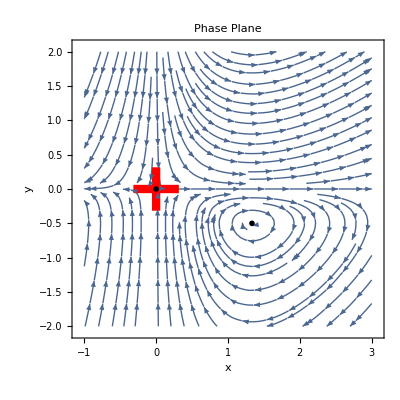

```mathematica
pplanePlot = StreamPlot[{f[x,y],g[x,y]},{x,-1,3},{y,-2,2},
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane"];

Show[pplanePlot,EVPlot,eqPtsPlot]
```

## Example #2

Consider the system given by 
ẋ =  2x (x-4) + 4x y
ẏ =  6xy - 8y
We would like to (1) conduct local analysis, and (2) graph the phase plane to validate our local analysis conclusions as before.

### Local Analysis

```mathematica
f2[x_,y_] = 2x (x-4)+ 4 x y;
g2[x_,y_] = 6x y - 8 y;
```

```mathematica
eqPts2 = Solve[{f2[x,y]==0,g2[x,y]==0},{x,y}]
```

{{x→4/3,y→4/3},{x→4,y→0},{x→0,y→0}}

```mathematica
DF2[xs_,ys_] = {{D[f2[x,y],x],D[f2[x,y],y]},{D[g2[x,y],x],D[g2[x,y],y]}}/.{x->xs,y->ys};
```

```mathematica
For[j = 1,j≤Length[eqPts2],j++,
Print[];
Print["==================================================================="];
Print["At the equilibrium point ",eqPts2[[j]]," the eigensystem is given by ",MatrixForm[Eigensystem[DF2[x,y]/.eqPts2[[j]]]]];
Print["===================================================================="];
Print[];
]
```

===================================================================

At the equilibrium point {x→4/3,y→4/3} the eigensystem is given by (8 | -16/3
{1,1} | {-2/3,1})

====================================================================

===================================================================

At the equilibrium point {x→4,y→0} the eigensystem is given by (16 | 8
{2,1} | {1,0})

====================================================================

===================================================================

At the equilibrium point {x→0,y→0} the eigensystem is given by (-8 | -8
{0,1} | {1,0})

====================================================================

### Comparing the Local Analysis with the Phase Plane

First, let’s create a loop that iterates over each of the equilibrium points.  We will plot the eigenvectors

```mathematica
For[j=1,j≤Length[eqPts2],j++,
esys = Eigensystem[DF2[x,y]/.eqPts2[[j]]];
Subscript[evPlots2, j]=ParametricPlot[esys[[2]]*s + Table[{x,y}/.eqPts2[[j]] ,{k,1,2}],{s,-1,1},
PlotStyle->{Red, Thickness->.015},
RegionFunction->Function[{u,v,vx,vy,n},(((u-x)^2+(v -y)^2)/.eqPts2[[j]])<.1]]];
EVPlot2 = Show[Table[Subscript[evPlots2, j],{j,1,Length[eqPts]}]];
eqPtsPlot2 = ListPlot[{x,y}/.eqPts2,
PlotMarkers->{Automatic,Scaled[.04]},
PlotStyle->Black];
```

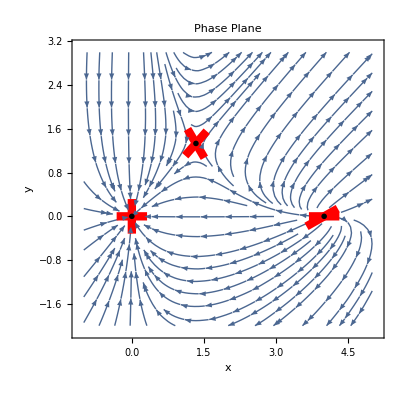

```mathematica
pplanePlot2 = StreamPlot[{f2[x,y],g2[x,y]},{x,-1,5},{y,-2,3},
FrameLabel->{"x","y"},
PlotLabel->"Phase Plane",
StreamPoints->400];

Show[pplanePlot2,EVPlot2,eqPtsPlot2]
```